# Analysis of data obtained with VASP

Authors: 
Group#1, School of Physical Science and Nanotechnology

## Part 1: The Si Atom

In this section we analyze the results of part1:

```mathematica
wrk="/home/angel/wrk/DFT/part1_si_atom";

SetDirectory[wrk]
```

/home/angel/wrk/DFT/part1_si_atom

```mathematica
data1=Import["cell1.dat"];
data1//TableForm
```

4. | 0.682732
5. | 0.314767
6. | 0.0478779
7. | -0.0821132
8. | -0.134517
9. | -0.153991
10. | -0.160899
11. | -0.163289
12. | -0.164077

The following data was obtained with spin-polarization in VARP (ISPIN=2)

```mathematica
data2=Import["cell2.dat"];
data2//TableForm
```

4. | -0.187866
5. | -0.48054
6. | -0.70674
7. | -0.816868
8. | -0.860159
9. | -0.876066
10. | -0.881249
11. | -0.882925
12. | -0.88364

```mathematica
{data1,data2}//ListLinePlot[#,
Mesh->Full,
PlotMarkers->{Automatic, 8},
Frame->True,
FrameLabel->{"Cell Length Å","Energy (eV)"},
Axes->False,
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
PlotStyle->{{Red,Thick},{Blue,Thick}},
InterpolationOrder->2,
ImageSize->400,
Epilog->{
Inset[
Panel[
Grid[{{"•","•"},{"ISPIN=1","ISPIN=2"}}//Transpose//Map[Style[#,15]&,#,{2}]&]
],
{Right,Top},{1.2,1.3}

]

}

]&
```

-Graphics-

HERE I WRITE MY NOTES AOBUT THE RESULT
In experiment we expect to have the blue line, the magnetic properties of the atom.  On the other hand, we should have some magnetic effects (ster-guerlak effect)

# Part 2: the Cl-ion

```mathematica
dataCi1=Import["/home/angel/wrk/DFT/part2_cl_ion/cell1.dat"];
data2//TableForm
```

data2

```mathematica
dataCi2=Import["/home/angel/wrk/DFT/part2_cl_ion/cell2.dat"];
dataCi2//TableForm
```

4. | -0.878292
6. | -3.65644
8. | -3.93381
10. | -3.97211
12. | -3.97904
14. | -3.98137
16. | -3.98286

```mathematica
{dataCi1,dataCi2}//ListLinePlot[#,
Mesh->Full,
PlotMarkers->{Automatic, 8},
Frame->True,
FrameLabel->{"Cell Length Å","Energy (eV)"},
Axes->False,
BaseStyle->{FontFamily->"Helvetica", FontSize->15},
PlotStyle->{{Red,Thick},{Blue,Thick}},
InterpolationOrder->1,
ImageSize->400,
Epilog->{
Inset[
Panel[
Grid[{{"•","•"},{"No IDIPOL","IDIPOL=4"}}//Transpose//Map[Style[#,15]&,#,{2}]&]
],
{Right,Top},{1.2,1.3}

]

}

]&
```

-Graphics-

We need to correct, first we need to check the convergence,we can see that the red line will converge but we shall increase the cell length, but, the blue line converges.

# Part 3: Silicon

```mathematica
dataSilicon=Import["/home/angel/wrk/DFT/part3_silicon/ecut.dat"];
dataSilicon//TableForm
```

200 | -11.8507
250 | -11.8805
300 | -11.8966
350 | -11.9009
400 | -11.9029
450 | -11.9033
500 | -11.9033
550 | -11.9034
600 | -11.9035
650 | -11.9036
700 | -11.9036
750 | -11.9036
800 | -11.9036
850 | -11.9037
900 | -11.9037

```mathematica
dataSiliconAtom=dataSilicon/.{x_,y_}:>{x,y/2}
```

{{200,-5.92534},{250,-5.94026},{300,-5.94829},{350,-5.95047},{400,-5.95147},{450,-5.95163},{500,-5.95164},{550,-5.95169},{600,-5.95176},{650,-5.95181},{700,-5.95182},{750,-5.95182},{800,-5.95182},{850,-5.95184},{900,-5.95185}}

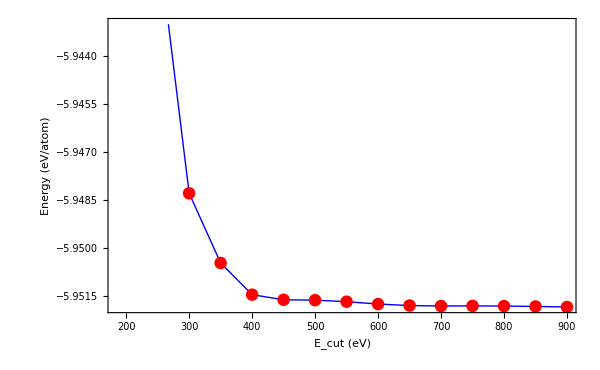

```mathematica
ListLinePlot[
dataSiliconAtom, 
PlotStyle->{Blue,Thick},
Mesh->All,MeshStyle->{Red,PointSize[0.015]},
AxesLabel->{"E_cut (eV)","Energy (eV/atom)"},
LabelStyle->{FontSize->16},
ImageSize->600,
Frame->True,
FrameLabel->{"E_cut (eV)","Energy (eV/atom)"},
FrameStyle->Directive[Black,16]
]
```

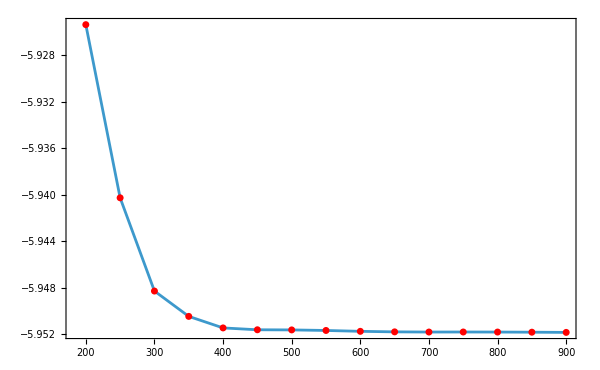

```mathematica
dataSiliconAtom//ListPlot[#,
Frame->True,
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->600,
Epilog->{Red,AbsolutePointSize[5],Point[#]}


]&
```

We need to know the convergence energy

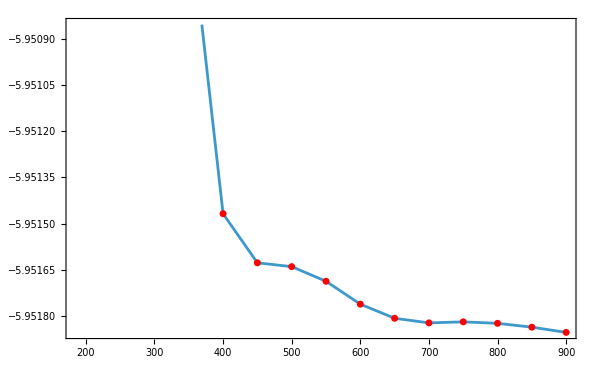

```mathematica
dataSiliconAtom//ListPlot[#,
Frame->True,
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",
FontSize->15},
Joined->True,
PlotRange->{#[[-1,2]],#[[-1,2]]+10^-3},
InterpolationOrder->1,
ImageSize->600,
Epilog->{Red,AbsolutePointSize[5],Point[#]}


]&
```

Then for this system the E_cutoff we will use is 400 eV. Do this test in any analysis. Here the point of convergence start at 400 eV, put this value in the INCAR file.

```mathematica
kpointSi=Import["/home/angel/wrk/DFT/part3_silicon/kps.dat"];
kpointSi//TableForm
```

3 | -11.2709
4 | -11.7089
5 | -11.836
6 | -11.8783
7 | -11.8936
8 | -11.8995
9 | -11.9019
10 | -11.903
11 | -11.9034
12 | -11.9036

### Analysis of k-points grids

```mathematica
datakp=Import["/home/angel/wrk/DFT/part3_silicon/kps.dat"]//Map[#/{1,2}&,#]&;
datakp//TableForm
```

3 | -5.63543
4 | -5.85444
5 | -5.91801
6 | -5.93916
7 | -5.94678
8 | -5.94976
9 | -5.95096
10 | -5.95151
11 | -5.9517
12 | -5.95181

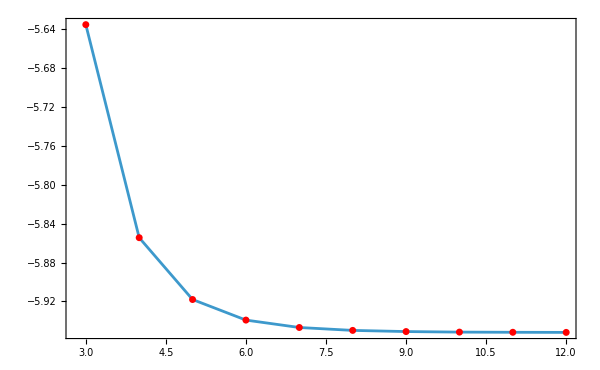

```mathematica
datakp//ListPlot[#,
Frame->True,
FrameLabel->{"",""},
BaseStyle->{FontFamily->"Helvetica",
FontSize->15},
Joined->True,
PlotRange->All,
InterpolationOrder->1,
ImageSize->600,
Epilog->{Red,AbsolutePointSize[5],Point[#]}


]&
```

Create the window (1 mili ev per atom) and see what is the energy convergence

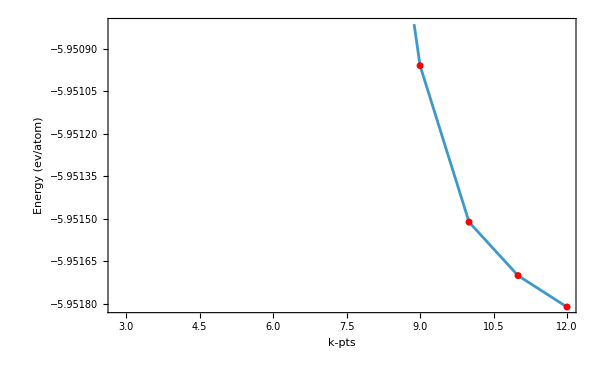

```mathematica
datakp//ListPlot[#,
Frame->True,
FrameLabel->{"k-pts","Energy (ev/atom)"},
BaseStyle->{FontFamily->"Helvetica",
FontSize->15},
Joined->True,
PlotRange->{#[[-1,2]],#[[-1,2]]+10^-3},
InterpolationOrder->1,
ImageSize->600,
Epilog->{Red,AbsolutePointSize[5],Point[#]}


]&
```

The energy converge is at 9. Then for this system a kp grid of 9x9x9 will be used

Now we are going to compute the Equation of state E(volume). Then make the plot lattice parameter vs the total energy. We need the volume vs energy

### The EOS for fcc silicon

the cross product is “esc croos esc”, and dot produc is “.”

```mathematica
a1= s{1/2,1/2,0};
a2= s{0,1/2,1/2};
a3= s{1/2,0,1/2};
(a1× a2).a3
```

s^3/4

```mathematica
cell=Import["/home/angel/wrk/DFT/part3_silicon/cell.dat"]//Map[{1/4 (# [[1]])^3,#[[2]]}&,#]&;
cell//TableForm
```

36.7995 | -11.8576
37.2192 | -11.876
37.6422 | -11.8909
38.0683 | -11.9024
38.4977 | -11.9106
38.9302 | -11.9156
39.366 | -11.9176
39.805 | -11.9166
40.2473 | -11.9128
40.6928 | -11.9062
41.1416 | -11.897
41.5938 | -11.8852
42.0492 | -11.871
42.5079 | -11.8544

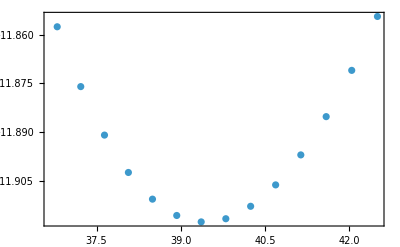

```mathematica
cell//ListPlot[#,Frame->True]&
```

EOS:

```mathematica
eos=e0 + (9 v0 B0)/16 (((v0/v)^(2/3)-1)^3 B0' + ((v0/v)^(2/3)-1)^2 (6-4 *(v0/v)^(2/3)))
```

e0+9/16 B0 v0 ((6-4 (v0/v)^(2/3)) (-1+(v0/v)^(2/3))^2+(-1+(v0/v)^(2/3))^3 B0')

```mathematica
nlm=NonlinearModelFit[cell,eos,{e0,v0,B0,B0'},v]
```

NonlinearModelFit::nrlnum: The function value {8.22051+0.0000174035 ⅈ,8.2389+0.0000172738 ⅈ,«11»,8.21734+0.0000158248 ⅈ} is not a list of real numbers with dimensions {14} at {e0,v0,B0,B0'} = {-3.63406,-0.0253016,0.224435,5.06106}.

FittedModel[…]

```mathematica
nlm["BestFitParameters"]
```

{e0→-3.63406,v0→-0.0253016,B0→0.224435,B0'→5.06106}

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1] +k [2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2
```

k[1]+k[2]/v^(2/3)+k[3]/v^(4/3)+k[4]/v^2

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm1=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm1["BestFitParameters"]
```

{k[1]→11.3426,k[2]→-498.554,k[3]→2185.47,k[4]→5427.48}

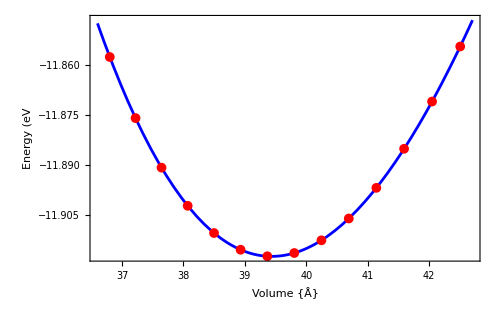

```mathematica
Plot[nlm1[v],{v,(cell[[All,1]]//Min)-0.2,
(cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume {Å}","Energy (eV"},
BaseStyle->{FontFamily->"Helvetica",
FontSize->15},
PlotRange->All,
ImageSize->500,
Epilog->{Red,AbsolutePointSize[7],Point[cell]},
Axes->None,
PlotStyle->{AbsoluteThickness[2],Blue}
]
```

```mathematica
nlm1["RSquared"]
```

1.

The optimal volume

```mathematica
opvol=FindMinimum[nlm[v],{v,39,40}]
```

{-12.0139,{v→3.23699}}

```mathematica
FindMinimum[nlm[v],{v,39,40}]
```

{-12.0139,{v→3.23699}}

To get the lattice parameter in this system we have:

```mathematica
Solve[vol==s^3/4,s]
```

{{s→(-2)^(2/3) vol^(1/3)},{s→2^(2/3) vol^(1/3)},{s→-(-1)^(1/3) 2^(2/3) vol^(1/3)}}

```mathematica
2^(2/3) v^(1/3)/.opvol[[2]]
```

2.34819

The bulk modulus B_0 is:

```mathematica
bulkm = v D[nlm1[v],{v,2}]/.opvol[[2]]
```

1320.58

```mathematica
UnitConvert[Quantity[bulkm,"Electronvolts"/("Angstroms")^3],"GigaPascals"]
```

211580. GPa

B_0’ is:

```mathematica
-v/bulkm D[v D[nlm1[v],{v,2}],v]/.opvol[[2]]
```

2.85751

```mathematica
sol=Solve[
{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B' == k[3]
-9/4 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[4]/.
nlm["BestFitParameters"],{e0,B0,B'}

}
]
```

Solve::naqs: e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1]&&45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2]&&(0.74411-1.28884 ⅈ)+(0.223233-0.386651 ⅈ) B'==«1»==k[4]&&{e0,B0,B'} is not a quantified system of equations and inequalities.

Solve[{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.74411-1.28884 ⅈ)+(0.223233-0.386651 ⅈ) B'==(-0.305689-0.529468 ⅈ)+k[3]-(0.229267+0.397101 ⅈ) B'==k[4],{e0,B0,B'}}]

```mathematica
acal=2^(2/3) v^(1/3)/.sol[[1]]
```

ReplaceAll::rmix: Elements of {e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.74411-1.28884 ⅈ)+(0.223233-0.386651 ⅈ) B'==«1»==k[4],{e0,B0,B'}} are a mixture of lists and nonlists.

2^(2/3) v^(1/3)/.{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.74411-1.28884 ⅈ)+(0.223233-0.386651 ⅈ) B'==(-0.305689-0.529468 ⅈ)+k[3]-(0.229267+0.397101 ⅈ) B'==k[4],{e0,B0,B'}}

The error of the predicted lattice parameter is:

```mathematica
(acal-aexp)/aexp 100/.{aexp->5.429}
```

18.4196 (-5.429+(2^(2/3) v^(1/3)/.{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.000683827-0.00118442 ⅈ)+(0.000205148-0.000355327 ⅈ) B'==(-8.15101×10^-6-0.000014118 ⅈ)+k[3]-(6.11326×10^-6+0.0000105885 ⅈ) B'==k[4],{e0,B0,B'}}))

# BULK MODEL, HOW DIFFICULT IS TO DEFORM A MATERIAL, THE PRESSION IS GETTING STRONG AND THIS MATERIAL IS HARD TO DEFROM.

## PART 4: THE SILICON CRYSTAL, FUNCTIONALS

### Results using PAW-PBE

the cross product is “esc croos esc”, and dot produc is “.”

```mathematica
a1= s{1/2,1/2,0};
a2= s{0,1/2,1/2};
a3= s{1/2,0,1/2};
(a1× a2).a3
```

s^3/4

```mathematica
cell=Import["/home/angel/wrk/DFT/part4_silicon2/part4_silicon2/cell-pbe.dat"]//Map[{1/4 (# [[1]])^3,#[[2]]}&,#]&;
cell//TableForm
```

39.366 | -10.8312
39.805 | -10.8397
40.2473 | -10.8452
40.4697 | -10.8469
40.6928 | -10.8478
40.9168 | -10.8481
41.1416 | -10.8477
41.3673 | -10.8466
41.5938 | -10.8448
42.0492 | -10.8394
42.5079 | -10.8315

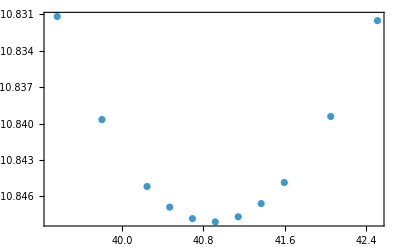

```mathematica
cell//ListPlot[#,Frame->True]&
```

EOS:

```mathematica
eos=e0 + (9 v0 B0)/16 (((v0/v)^(2/3)-1)^3 B0' + ((v0/v)^(2/3)-1)^2 (6-4 *(v0/v)^(2/3)))
```

e0+9/16 B0 v0 ((6-4 (v0/v)^(2/3)) (-1+(v0/v)^(2/3))^2+(-1+(v0/v)^(2/3))^3 B0')

```mathematica
nlm=NonlinearModelFit[cell,eos,{e0,v0,B0,B0'},v]
```

NonlinearModelFit[cell,e0+9/16 B0 v0 ((6-4 (v0/v)^(2/3)) (-1+(v0/v)^(2/3))^2+(-1+(v0/v)^(2/3))^3 B0'),{e0,v0,B0,B0'},v]

```mathematica
nlm["BestFitParameters"]
```

{e0→-10.6152,v0→0.046813,B0→1.55915,B0'→-0.36226}

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0-(27 B0 v0)/8-9/16 B0 v0 B0'+(9 B0 v0^3 B0')/(16 v^2)+(45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(-9/4 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)

```mathematica
model=k[1] +k [2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2
```

k[1]+k[2]/v^(2/3)+k[3]/v^(4/3)+k[4]/v^2

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm1=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm1["BestFitParameters"]
```

{k[1]→10.6771,k[2]→-462.854,k[3]→1890.12,k[4]→6779.21}

```mathematica
Plot[nlm1[v],{v,(cell[[All,1]]//Min)-0.2,
(cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume {Å}","Energy (eV"},
BaseStyle->{FontFamily->"Helvetica",
FontSize->15},
PlotRange->All,
ImageSize->500,
Epilog->{Red,AbsolutePointSize[7],Point[cell]},
Axes->None,
PlotStyle->{AbsoluteThickness[2],Blue}
]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Plot::plln: Limiting value -0.2+Symbol[] in {v,-0.2+Symbol[],0.2+Symbol[]} is not a machine-sized real number.

Plot[nlm1[v],{v,Min[cell⟦All,1⟧]-0.2,Max[cell⟦All,1⟧]+0.2},Frame→True,FrameLabel→{Volume {Å},Energy (eV},BaseStyle→{FontFamily→Helvetica,FontSize→15},PlotRange→All,ImageSize→500,Epilog→{Red,AbsolutePointSize[7],Point[cell]},Axes→None,PlotStyle→{AbsoluteThickness[2],Blue}]

```mathematica
nlm1["RSquared"]
```

1.

The optimal volume

```mathematica
opvol=FindMinimum[nlm[v],{v,39,40}]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum[nlm[v],{v,39,40}]

```mathematica
FindMinimum[nlm[v],{v,39,40}]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum[nlm[v],{v,39,40}]

To get the lattice parameter in this system we have:

```mathematica
Solve[vol==s^3/4,s]
```

{{s→(-2)^(2/3) vol^(1/3)},{s→2^(2/3) vol^(1/3)},{s→-(-1)^(1/3) 2^(2/3) vol^(1/3)}}

```mathematica
2^(2/3) v^(1/3)/.opvol[[2]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ReplaceAll::reps: {v,39,40} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2^(2/3) v^(1/3)/.{v,39,40}

The bulk modulus B_0 is:

```mathematica
bulkm = v D[nlm1[v],{v,2}]/.opvol[[2]]
```

FindMinimum::nrnum: The function value -11.893-0.00016036 ⅈ is not a real number at {v} = {39.}.

ReplaceAll::reps: {v,39,40} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(32564.9/v^4+6799.22/v^(10/3)-553.949/v^(8/3)) v/.{v,39,40}

```mathematica
UnitConvert[Quantity[bulkm,"Electronvolts"/("Angstroms")^3],"GigaPascals"]
```

(801088317 ((32564.9/v^4+6799.22/v^(10/3)-553.949/v^(8/3)) v/.{v,39,40}))/5000000 GPa

B_0’ is:

```mathematica
-v/bulkm D[v D[nlm1[v],{v,2}],v]/.opvol[[2]]
```

FindMinimum::nrnum: The function value -11.893-0.00016036 ⅈ is not a real number at {v} = {39.}.

ReplaceAll::reps: {v,39,40} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(v (32564.9/v^4+6799.22/v^(10/3)-553.949/v^(8/3)+(-130260./v^5-22664.1/v^(13/3)+1477.2/v^(11/3)) v))/((32564.9/v^4+6799.22/v^(10/3)-553.949/v^(8/3)) v/.{v,39,40})/.{v,39,40}

```mathematica
e0-(27 B0 v0)/8-9/16 B0 v0 B0'+(9 B0 v0^3 B0')/(16 v^2)+(45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(-9/4 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)
```

e0-(27 B0 v0)/8-9/16 B0 v0 B0'+(9 B0 v0^3 B0')/(16 v^2)+(45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(-9/4 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)

```mathematica
sol=Solve[
{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B' == k[3]
-9/4 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[4]/.
nlm["BestFitParameters"],{e0,B0,B'}

}
]
```

Solve::naqs: e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1]&&45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2]&&(0.000683827-0.00118442 ⅈ)+(0.000205148-0.000355327 ⅈ) B'==(-8.15101×10^-6-0.000014118 ⅈ)+k[3]-(6.11326×10^-6+«23» ⅈ) B'==k[4]&&{e0,B0,B'} is not a quantified system of equations and inequalities.

Solve[{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.000683827-0.00118442 ⅈ)+(0.000205148-0.000355327 ⅈ) B'==(-8.15101×10^-6-0.000014118 ⅈ)+k[3]-(6.11326×10^-6+0.0000105885 ⅈ) B'==k[4],{e0,B0,B'}}]

```mathematica
acal=2^(2/3) v^(1/3)/.sol[[1]]
```

ReplaceAll::rmix: Elements of {e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.000683827-0.00118442 ⅈ)+(0.000205148-0.000355327 ⅈ) B'==(-8.15101×10^-6-0.000014118 ⅈ)+k[3]-(6.11326×10^-6+«23» ⅈ) B'==k[4],{e0,B0,B'}} are a mixture of lists and nonlists.

2^(2/3) v^(1/3)/.{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.000683827-0.00118442 ⅈ)+(0.000205148-0.000355327 ⅈ) B'==(-8.15101×10^-6-0.000014118 ⅈ)+k[3]-(6.11326×10^-6+0.0000105885 ⅈ) B'==k[4],{e0,B0,B'}}

The error of the predicted lattice parameter is:

```mathematica
(acal-aexp)/aexp 100/.{aexp->5.429}
```

18.4196 (-5.429+(2^(2/3) v^(1/3)/.{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.000683827-0.00118442 ⅈ)+(0.000205148-0.000355327 ⅈ) B'==(-8.15101×10^-6-0.000014118 ⅈ)+k[3]-(6.11326×10^-6+0.0000105885 ⅈ) B'==k[4],{e0,B0,B'}}))

# BULK MODEL, HOW DIFFICULT IS TO DEFORM A MATERIAL, THE PRESSION IS GETTING STRONG AND THIS MATERIAL IS HARD TO DEFROM.

### Results with PAW-PBESOL

the cross product is “esc croos esc”, and dot produc is “.”

```mathematica
a1= s{1/2,1/2,0};
a2= s{0,1/2,1/2};
a3= s{1/2,0,1/2};
(a1× a2).a3
```

s^3/4

```mathematica
cell=Import["/home/angel/wrk/DFT/part3_silicon/cell.dat"]//Map[{1/4 (# [[1]])^3,#[[2]]}&,#]&;
cell//TableForm
```

36.7995 | -11.8576
37.2192 | -11.876
37.6422 | -11.8909
38.0683 | -11.9024
38.4977 | -11.9106
38.9302 | -11.9156
39.366 | -11.9176
39.805 | -11.9166
40.2473 | -11.9128
40.6928 | -11.9062
41.1416 | -11.897
41.5938 | -11.8852
42.0492 | -11.871
42.5079 | -11.8544

```mathematica
cell//ListPlot[#,Frame->True]&
```

-Graphics-

EOS:

```mathematica
eos=e0 + (9 v0 B0)/16 (((v0/v)^(2/3)-1)^3 B0' + ((v0/v)^(2/3)-1)^2 (6-4 *(v0/v)^(2/3)))
```

e0+9/16 B0 v0 ((6-4 (v0/v)^(2/3)) (-1+(v0/v)^(2/3))^2+(-1+(v0/v)^(2/3))^3 B0')

```mathematica
nlm=NonlinearModelFit[cell,Re[eos],{e0,v0,B0,B0'},v]
```

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FittedModel[…]

```mathematica
nlm["BestFitParameters"]
```

{e0→-11.2766,v0→-1.04081,B0→0.247508,B0'→2.13431}

```mathematica
eos//PowerExpand//ExpandAll//Collect[#,v]&
```

e0+(27 B0 v0)/8-9/16 B0 v0 B0'+(-9 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(63/8 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)+(-(9 B0 v0^3)/4+9/16 B0 v0^3 B0')/v^2

```mathematica
model=k[1] +k [2] v^(-2/3)+k[3] v^(-4/3)+k[4] v^-2
```

k[1]+k[2]/v^(2/3)+k[3]/v^(4/3)+k[4]/v^2

```mathematica
parameters=Table[k[i],{i,4}]
```

{k[1],k[2],k[3],k[4]}

```mathematica
nlm1=NonlinearModelFit[cell,model,parameters,v]
```

FittedModel[…]

```mathematica
nlm1["BestFitParameters"]
```

{k[1]→11.3426,k[2]→-498.554,k[3]→2185.47,k[4]→5427.48}

```mathematica
Plot[nlm1[v],{v,(cell[[All,1]]//Min)-0.2,
(cell[[All,1]]//Max)+0.2},
Frame->True,
FrameLabel->{"Volume {Å}","Energy (eV"},
BaseStyle->{FontFamily->"Helvetica",
FontSize->15},
PlotRange->All,
ImageSize->500,
Epilog->{Red,AbsolutePointSize[7],Point[cell]},
Axes->None,
PlotStyle->{AbsoluteThickness[2],Blue}
]
```

Symbol::argx: Symbol called with 0 arguments; 1 argument is expected.

General::stop: Further output of Symbol::argx will be suppressed during this calculation.

Plot::plln: Limiting value -0.2+Symbol[] in {v,-0.2+Symbol[],0.2+Symbol[]} is not a machine-sized real number.

Plot[nlm1[v],{v,Min[cell⟦All,1⟧]-0.2,Max[cell⟦All,1⟧]+0.2},Frame→True,FrameLabel→{Volume {Å},Energy (eV},BaseStyle→{FontFamily→Helvetica,FontSize→15},PlotRange→All,ImageSize→500,Epilog→{Red,AbsolutePointSize[7],Point[cell]},Axes→None,PlotStyle→{AbsoluteThickness[2],Blue}]

```mathematica
nlm1["RSquared"]
```

1.

The optimal volume

```mathematica
opvol=FindMinimum[nlm[v],{v,39,40}]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

FindMinimum[nlm[v],{v,39,40}]

```mathematica
FindMinimum[nlm[v],{v,39,40}]
```

FindMinimum::nrnum: The function value -11.893-0.00016036 ⅈ is not a real number at {v} = {39.}.

FindMinimum[nlm[v],{v,39,40}]

To get the lattice parameter in this system we have:

```mathematica
Solve[vol==s^3/4,s]
```

{{s→(-2)^(2/3) vol^(1/3)},{s→2^(2/3) vol^(1/3)},{s→-(-1)^(1/3) 2^(2/3) vol^(1/3)}}

```mathematica
2^(2/3) v^(1/3)/.opvol[[2]]
```

FindMinimum::nrnum: The function value -11.893-0.00016036 ⅈ is not a real number at {v} = {39.}.

ReplaceAll::reps: {v,39,40} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

2^(2/3) v^(1/3)/.{v,39,40}

The bulk modulus B_0 is:

```mathematica
bulkm = v D[nlm1[v],{v,2}]/.opvol[[2]]
```

FindMinimum::nrnum: The function value -11.893-0.00016036 ⅈ is not a real number at {v} = {39.}.

ReplaceAll::reps: {v,39,40} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

(32564.9/v^4+6799.22/v^(10/3)-553.949/v^(8/3)) v/.{v,39,40}

```mathematica
UnitConvert[Quantity[bulkm,"Electronvolts"/("Angstroms")^3],"GigaPascals"]
```

(801088317 ((32564.9/v^4+6799.22/v^(10/3)-553.949/v^(8/3)) v/.{v,39,40}))/5000000 GPa

B_0’ is:

```mathematica
-v/bulkm D[v D[nlm1[v],{v,2}],v]/.opvol[[2]]
```

FindMinimum::nrnum: The function value -11.893-0.00016036 ⅈ is not a real number at {v} = {39.}.

ReplaceAll::reps: {v,39,40} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

-(v (32564.9/v^4+6799.22/v^(10/3)-553.949/v^(8/3)+(-130260./v^5-22664.1/v^(13/3)+1477.2/v^(11/3)) v))/((32564.9/v^4+6799.22/v^(10/3)-553.949/v^(8/3)) v/.{v,39,40})/.{v,39,40}

```mathematica
e0-(27 B0 v0)/8-9/16 B0 v0 B0'+(9 B0 v0^3 B0')/(16 v^2)+(45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(-9/4 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)
```

e0-(27 B0 v0)/8-9/16 B0 v0 B0'+(9 B0 v0^3 B0')/(16 v^2)+(45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B0')/v^(2/3)+(-9/4 B0 v0^(7/3)-27/16 B0 v0^(7/3) B0')/v^(4/3)

```mathematica
sol=Solve[
{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],
45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],
45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B' == k[3]
-9/4 B0 v0^(7/3)-27/16 B0 v0^(7/3) B'==k[4]/.
nlm["BestFitParameters"],{e0,B0,B'}

}
]
```

Solve::naqs: e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1]&&45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2]&&(0.000683827-0.00118442 ⅈ)+(0.000205148-0.000355327 ⅈ) B'==(-8.15101×10^-6-0.000014118 ⅈ)+k[3]-(6.11326×10^-6+«23» ⅈ) B'==k[4]&&{e0,B0,B'} is not a quantified system of equations and inequalities.

Solve[{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.000683827-0.00118442 ⅈ)+(0.000205148-0.000355327 ⅈ) B'==(-8.15101×10^-6-0.000014118 ⅈ)+k[3]-(6.11326×10^-6+0.0000105885 ⅈ) B'==k[4],{e0,B0,B'}}]

```mathematica
acal=2^(2/3) v^(1/3)/.sol[[1]]
```

ReplaceAll::rmix: Elements of {e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.000683827-0.00118442 ⅈ)+(0.000205148-0.000355327 ⅈ) B'==(-8.15101×10^-6-0.000014118 ⅈ)+k[3]-(6.11326×10^-6+«23» ⅈ) B'==k[4],{e0,B0,B'}} are a mixture of lists and nonlists.

2^(2/3) v^(1/3)/.{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.000683827-0.00118442 ⅈ)+(0.000205148-0.000355327 ⅈ) B'==(-8.15101×10^-6-0.000014118 ⅈ)+k[3]-(6.11326×10^-6+0.0000105885 ⅈ) B'==k[4],{e0,B0,B'}}

The error of the predicted lattice parameter is:

```mathematica
(acal-aexp)/aexp 100/.{aexp->5.429}
```

18.4196 (-5.429+(2^(2/3) v^(1/3)/.{e0-(27 B0 v0)/8-9/16 B0 v0 B'==k[1],45/8 B0 v0^(5/3)+27/16 B0 v0^(5/3) B'==k[2],(0.000683827-0.00118442 ⅈ)+(0.000205148-0.000355327 ⅈ) B'==(-8.15101×10^-6-0.000014118 ⅈ)+k[3]-(6.11326×10^-6+0.0000105885 ⅈ) B'==k[4],{e0,B0,B'}}))

# BULK MODEL, HOW DIFFICULT IS TO DEFORM A MATERIAL, THE PRESSION IS GETTING STRONG AND THIS MATERIAL IS HARD TO DEFROM.

CHeck the error in bulk modulus

```mathematica
(Bcal -Bexpt)/Bexpt 100/.{Bcal->89.09,Bexpt->98}
```

-9.09184